{a→0.572086,s→0.0835606,m1→140.286,m2→140.468,ac→0.000241272,mc→140.5,sc→0.5005}

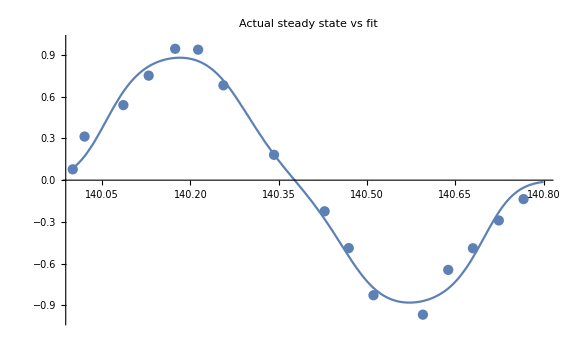

steadystateplot.png

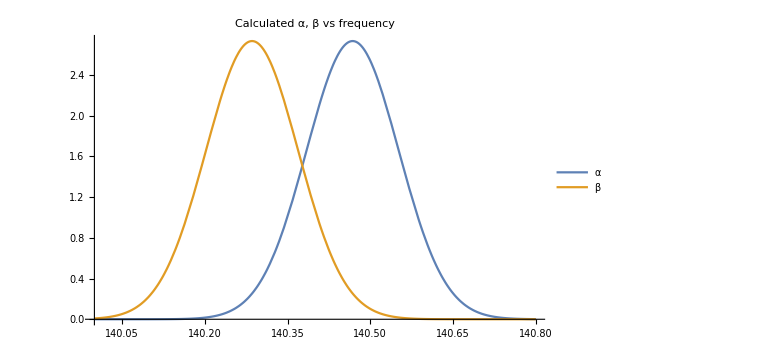

alphabetaplot.png

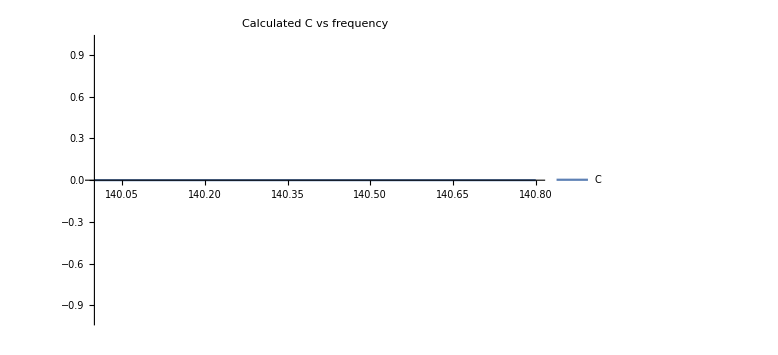

```mathematica
ClearAll["Global`*"];
(* The steady state function and some good values for Subscript[T, 1e] and Subscript[T, 1n] *)
physicalTimes={t1e->0.03,t1n->50*60};
pssnPhysical[a_,b_,c_]=(c t1n(b-a))/(t1e(2+a+b)+c t1n(a+b+2a b))/.physicalTimes;

(* Try to model the steady state as a function of frequency *)
(* Here are a list of distributions to use in getting α,β in terms of frequency *)
gaussian[m_,s_,x_]=PDF[NormalDistribution[m,s],x];
cauchy[m_,s_,x_]=PDF[CauchyDistribution[m,s],x];
studentT2[m_,s_,x_]=PDF[StudentTDistribution[m,s,2],x];
studentT3[m_,s_,x_]=PDF[StudentTDistribution[m,s,3],x];
dist1[m_,s_,x_]=Exp[-Abs[(x-m)/s]];
dist21[m_,s_,x_]=gaussian[m-s,s,x]+gaussian[m+s,s,x];
dist22[m_,s_,x_]=gaussian[m-s,s/2,x]+gaussian[m+s,s/2,x];
constant[m_,s_,x_]=1;
(* Choose distribution here *)
distribution=gaussian;
cDistribution=constant;
(* Compute alpha, beta distributions *)
alphaDist[a_,m2_,s_,x_]=a distribution[m2,s,x];
betaDist[a_,m1_,s_,x_]=a distribution[m1,s,x];
cDist[ac_,mc_,sc_,x_]=ac cDistribution[mc,sc,x];

(* Set up steady state function *)
pssnDistribution[a_,s_,m1_,m2_,ac_,mc_,sc_,x_]=pssnPhysical[alphaDist[a,m2,s,x],betaDist[a,m1,s,x],cDist[ac,mc,sc,x]];
(* The real steady state data *)
realDataList={{140,0.191317},{140.02,0.770378},{140.086,1.32606},{140.129,1.84658},{140.174,2.32045},{140.213,2.30471},{140.256,1.67516},{140.342,0.447462},{140.428,-0.549817},{140.469,-1.19995},{140.511,-2.03283},{140.553,-2.70277},{140.595,-2.37594},{140.638,-1.58521},{140.68,-1.20299},{140.724,-0.711866},{140.766,-0.334842}};
(* Normalized real data *)
maxSteadyState=1.1;
realDataListAdj=Map[Function[list,{list[[1]],list[[2]]/(2.70277/maxSteadyState)}],realDataList];

(* Calculate a fit for the various parameters *)
bestFit=FindFit[realDataListAdj,{pssnDistribution[a,s,m1,m2,ac,mc,sc,x],
{0≤a≤5,0.001≤s≤1,0.01*^-4≤ac≤100*^-4,140.2≤m1≤140.6,140.2≤m2≤140.6,140≤mc≤141,0.001≤sc≤1}},
{a,s,m1,m2,ac,mc,sc},x]

(* Show some useful plots *)
steadyStatePlot=Show[ListPlot[realDataListAdj],Plot[pssnDistribution[a,s,m1,m2,ac,mc,sc,x]/.bestFit,{x,140,140.8}],
PlotRange->{{140,140.8},{-1,1}},
ImageSize->Large,
PlotLabel->"Actual steady state vs fit"]
Export["steadystateplot.png",steadyStatePlot]
(* Plot α and β vs frequency *)
alphaBetaPlot=Plot[{alphaDist[a,m2,s,x]/.bestFit,betaDist[a,m1,s,x]/.bestFit},{x,140,140.8},
PlotRange->All,ImageSize->Large,PlotLegends->{"α","β"},
PlotLabel->"Calculated α, β vs frequency"]
Export["alphabetaplot.png",alphaBetaPlot]
(* Plot c vs frequency *)
Plot[cDist[ac,mc,sc,x]/.bestFit,{x,140,140.8},
PlotRange->All,ImageSize->Large,PlotLegends->{"C"},
PlotLabel->"Calculated C vs frequency"]
```

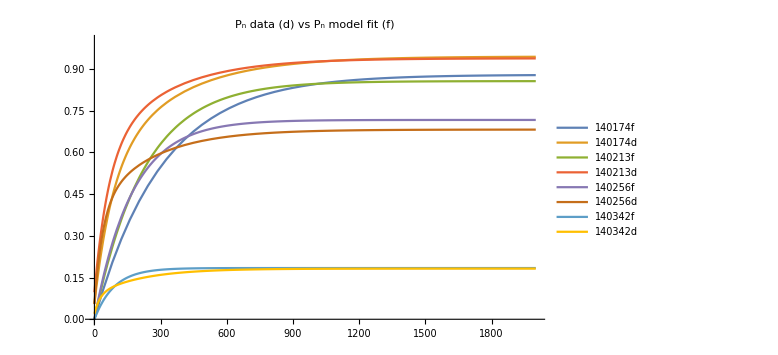

comparisonplot.png

```mathematica
(* These take the equations for Subscript[P, n] and Subscript[P, e] and make them more "regular" *)
constToParam={aa->aConst,bb->bConst,cc->cConst,dd->dConst};
aConst=-t1e/t1n-(c α)/2-(c β)/2;
bConst=(c α)/2-(c β)/2;
cConst=α/2-β/2;
dConst=-1-α/2-β/2;
(* These correspond to coefficients in the decoupled equation for Subscript[P, n]
(a system of two linear first-order ODEs is transformed into a single linear second-order ODE) *)
simplToConst={aaa->aSimpl,bbb->bSimpl,ccc->cSimpl, pn0->pn0Simpl};
aSimpl=t1e^2/bb;
bSimpl=-t1e aa/bb-t1e dd/bb;
cSimpl=aa dd/bb-cc;
pn0Simpl=-bb/t1e;
eqnDecouple={aaa pn''[t]+bbb pn'[t]+ccc pn[t]+1==0,
pn[0]==0,pn'[0]==pn0};
solDecouple=DSolve[eqnDecouple,pn[t],t];
(* Subscript[P, n] in terms of simplified aaa, bbb, etc. *)
pnSimpl[t_]=pn[t]/.solDecouple;
(* Subscript[P, n] in terms of constants aa, bb, etc. *)
pnConst[t_]=pnSimpl[t]/.simplToConst;
(* Subscript[P, n] in terms of actual parameters α, β, etc. *)
pnParam[t_]=pnConst[t]/.constToParam;
(* Subscript[P, n] with physical time parameters *)
pnPhysical[t_]=pnParam[t]/.physicalTimes;

(* Some real data *)
pnData[a_,c1_,k1_,c2_,k2_]=(a+c1 Exp[-k1 t]+c2 Exp[-k2 t])/(2.70277/maxSteadyState);
p140086[t_]=pnData[1.32606,-7.48407,0.00116616,6.20027,0.00116616];
p140129[t_]=pnData[1.84658,-1.78546,0.0021399,0,0];
p140174[t_]=pnData[2.32045,-1.10749,0.0124691,-1.07449,0.00310825];
p140213[t_]=pnData[2.30471,-1.18262,0.0156939,-0.883323,0.00341633];
p140256[t_]=pnData[1.67516,-0.84578,0.0265268,-0.696076,0.00398314];
p140342[t_]=pnData[0.447462,-0.16541,0.0406766,-0.233527,0.00479694];
(* The solution from above *)
pnBestFit[f_,t_]=pnPhysical[t]/.{α->alphaDist[a,m2,s,f],β->betaDist[a,m1,s,f],c->cDist[ac,mc,sc,f]}/.bestFit;
(* Try to graph this solution using the best fit *)
comparisonPlot=Plot[{pnBestFit[140.174,t],p140174[t],
pnBestFit[140.213,t],p140213[t],
pnBestFit[140.256,t],p140256[t],
pnBestFit[140.342,t],p140342[t]},
{t,0,2000},PlotRange->{{0,2000},{0,1}},ImageSize->Large,PlotLegends->{"140174f","140174d","140213f","140213d","140256f","140256d","140342f","140342d"},
PlotLabel->"P_n data (d) vs P_n model fit (f)"]
Export["comparisonplot.png",comparisonPlot]
```

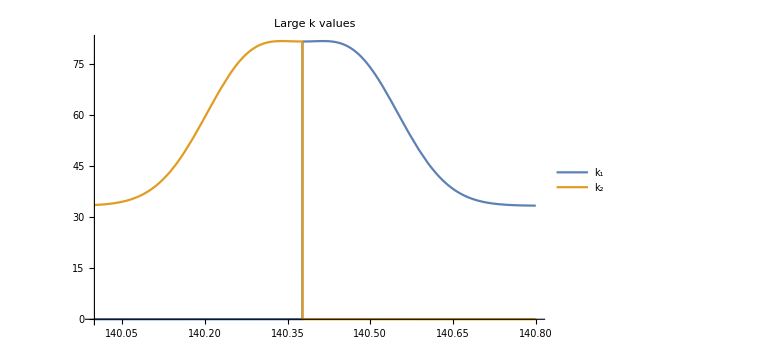

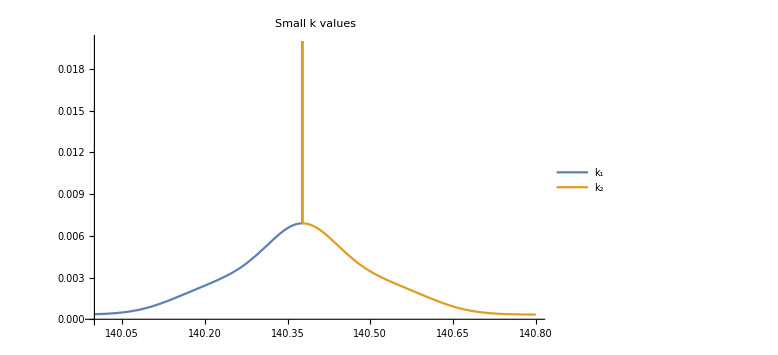

```mathematica
(* The values Subscript[k, 1] and Subscript[k, 2] (rates) *)
k1Rate=(bbb+Sqrt[bbb^2-4aaa ccc])/(2aaa);
k2Rate=(bbb-Sqrt[bbb^2-4aaa ccc])/(2aaa);
Plot[{k1Rate/.simplToConst/.constToParam/.physicalTimes/.{α->alphaDist[a,m2,s,f],β->betaDist[a,m1,s,f],c->cDist[ac,mc,sc,f]}/.bestFit,
k2Rate/.simplToConst/.constToParam/.physicalTimes/.{α->alphaDist[a,m2,s,f],β->betaDist[a,m1,s,f],c->cDist[ac,mc,sc,f]}/.bestFit},
{f,140,140.8},
PlotLegends->{"k_1","k_2"},
ImageSize->Large,
PlotLabel->"Large k values"]
(* A zoomed in plot on the smaller k *)
Plot[{k1Rate/.simplToConst/.constToParam/.physicalTimes/.{α->alphaDist[a,m2,s,f],β->betaDist[a,m1,s,f],c->cDist[ac,mc,sc,f]}/.bestFit,
k2Rate/.simplToConst/.constToParam/.physicalTimes/.{α->alphaDist[a,m2,s,f],β->betaDist[a,m1,s,f],c->cDist[ac,mc,sc,f]}/.bestFit},
{f,140,140.8},
PlotLegends->{"k_1","k_2"},
ImageSize->Large,
PlotRange->{{140,140.8},{0,0.02}},
PlotLabel->"Small k values"]
```

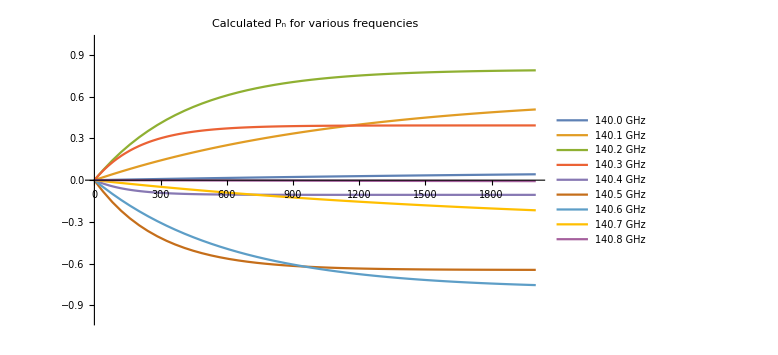

variouspnplot.png

```mathematica
(* Plot the best fit for some values *)
fRange=Range[140,140.8,0.1];
variousPnPlot=Plot[Evaluate[Table[pnBestFit[f,t],{f,fRange}]],{t,0,2000},
PlotRange->{{0,2000},{-1,1}},ImageSize->Large,
PlotLegends->Evaluate[Table[ToString@StringForm["`` GHz",NumberForm[f,{4,1}]],{f,fRange}]],
PlotLabel->"Calculated P_n for various frequencies"]
Export["variouspnplot.png",variousPnPlot]
```

```mathematica
alphaDist[aa,mm2,ss,ff]
betaDist[aa,mm1,ss,ff]
```

(aa ⅇ^(-(ff-mm2)^2/(2 ss^2)))/(√(2 π) ss)

(aa ⅇ^(-(ff-mm1)^2/(2 ss^2)))/(√(2 π) ss)

```mathematica
realDataListAdj
```

{{140,0.0778641},{140.02,0.313536},{140.086,0.539693},{140.129,0.751539},{140.174,0.9444},{140.213,0.937994},{140.256,0.681773},{140.342,0.182112},{140.428,-0.22377},{140.469,-0.488367},{140.511,-0.827341},{140.553,-1.1},{140.595,-0.966984},{140.638,-0.645164},{140.68,-0.489605},{140.724,-0.289722},{140.766,-0.136277}}